```mathematica
M:={{-k01,k10,0},{k01,-k10 - k12,k21},{1,1,1}}
```

```mathematica
b:={0,0,1}
LinearSolve[M,b]
```

{(k10 k21)/(k01 k12+k01 k21+k10 k21),(k01 k21)/(k01 k12+k01 k21+k10 k21),(k01 k12)/(k01 k12+k01 k21+k10 k21)}

```mathematica
M:={{-2p,e,0},{2p,-e - p,2e},{1,1,1}}
b:={0,0,1}
LinearSolve[M,b]
```

{e^2/(e+p)^2,(2 e p)/(e+p)^2,p^2/(e+p)^2}

```mathematica
FullSimplify[(2 e + p)/(2 e^2)]
```

(2 e+p)/(2 e^2)

```mathematica
Plot3D[(2 e+p)/(2 e^2),{e,0,20.},{p,1,20.}]
```

```mathematica
Sum[Product[((NN-i)p)/((i+1)e),{i,0,n}],{n,0,NN-1}]
```

-1+((e+p)/e)^NN

```mathematica
Simplify[1/e(EulerGamma p-n p+EulerGamma NN p+p PolyGamma[0,1+n]+NN p PolyGamma[0,1+n])]
```

(p (EulerGamma-n+EulerGamma NN+(1+NN) PolyGamma[0,1+n]))/e

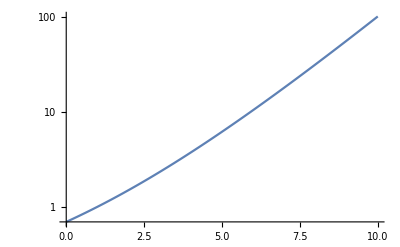

```mathematica
LogPlot[(1/x)((1+1)^x - 1),{x,0,10}]
```

```mathematica
1^10
```

1

```mathematica
f[x_]:=(1/(Sqrt[4 π D t]))Exp[-x^2/(4 D t)]
```

```mathematica
Integrate[x^2 f[x],{x,-Infinity,Infinity}]
```

ConditionalExpression[2 √(1/(D t)) (D t)^(3/2), Re[1/(D t)]>0]

```mathematica
FullSimplify[2 √(1/D) (D)^(3/2),Assumptions->D>0]
```

2 D

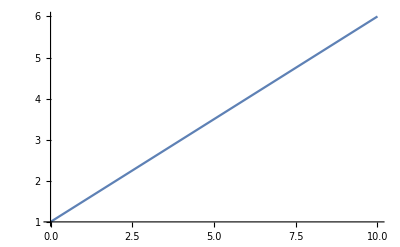

```mathematica
Plot[(1+0.5x),{x,0,10}]
```

```mathematica
M:={{-k01,k10,0},{k01,-k10 - k12,k21},{1,1,1}}
b:={0,0,1}
LinearSolve[M,b]
```

{(k10 k21)/(k01 k12+k01 k21+k10 k21),(k01 k21)/(k01 k12+k01 k21+k10 k21),(k01 k12)/(k01 k12+k01 k21+k10 k21)}